```mathematica
eqn=y''[z]-z*y[z]+ϵ*y[z]==0
```

-z y[z]+ϵ y[z]+y''[z]==0

```mathematica
sol=DSolve[eqn,y[z],z]
```

{{y[z]→AiryAi[z-ϵ] C[1]+AiryBi[z-ϵ] C[2]}}

```mathematica
zRango={z, -15, 5}
```

{z,-15,5}

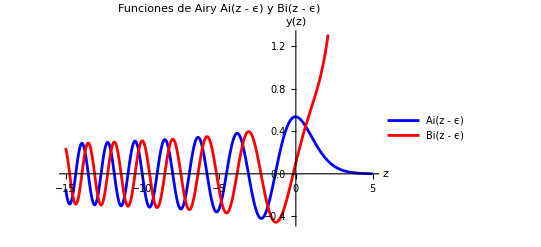

```mathematica
Plot[{AiryAi[z-1],AiryBi[z-1]},zRango,PlotLabel->"Funciones de Airy Ai(z - ϵ) y Bi(z - ϵ)",AxesLabel->{"z","y(z)"},PlotLegends->{"Ai(z - ϵ)","Bi(z - ϵ)"},PlotStyle->{Blue,Red}]
```

```mathematica
epsilon1=ϵ/. FindRoot[AiryAi[-ϵ]==0,{ϵ,2}]
```

2.33811

```mathematica
epsilonList=Table[ϵ/. FindRoot[AiryAi[-ϵ]==0,{ϵ,n+1}],{n,2,12}]
```

{2.33811,4.08795,4.08795,5.52056,6.78671,7.94413,9.02265,10.0402,11.0085,11.936,12.8288}

```mathematica
y1[z_]:=AiryAi[z-epsilon1]
```

```mathematica
norm1=Sqrt[NIntegrate[y1[z]^2,{z,0,Infinity}]]
```

0.701211

```mathematica
c1 = 1/norm1
```

1.4261

```mathematica
y1Normal[z_]:=y1[z]/norm1
```

```mathematica
y10[z_]:=AiryAi[z-epsilonList[[11]]]
```

```mathematica
norm10=Sqrt[NIntegrate[y10[z]^2,{z,0,Infinity}]]
```

1.06779

```mathematica
c10 = 1/norm10
```

0.93651

```mathematica
y10Normal[z_]:=y10[z]/norm10
```

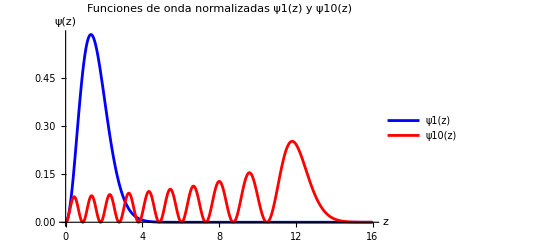

```mathematica
Plot[{y1Normal[z]^2,y10Normal[z]^2},{z,0,16},PlotLabel->"Funciones de onda normalizadas ψ1(z) y ψ10(z)",AxesLabel->{"z","ψ(z)"},PlotLegends->{"ψ1(z)","ψ10(z)"},PlotStyle->{Blue,Red}, PlotRange->Full]
```

```mathematica
ortogonal=Re[NIntegrate[y1Normal[z]*y10Normal[z],{z,0,Infinity}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.72352}. NIntegrate obtained -8.86877×10^-17 and 1.56187×10^-16 for the integral and error estimates.

-8.86877×10^-17

```mathematica
m = 1
```

1

```mathematica
hbar = 1
```

1

```mathematica
g = 1
```

1

```mathematica
a=(2*m^2*g/hbar^2)^(1/3)
```

2^(1/3)

```mathematica
x1[z_]:=z/a
```

```mathematica
x1Med=NIntegrate[x1[z]*Abs[y1Normal[z]]^2,{z,0,Infinity}]
```

1.23717

```mathematica
x1SqrMed=NIntegrate[x1[z]^2*Abs[y1Normal[z]]^2,{z,0,Infinity}]
```

1.83671

```mathematica
sigmaX1=Sqrt[x1SqrMed-x1Med^2]
```

0.55328

```mathematica
p1Med=Re[-I*hbar*NIntegrate[Conjugate[y1Normal[z]]*D[y1Normal[z],z],{z,0,Infinity}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.2858}. NIntegrate obtained -7.80626×10^-18 and 7.65428×10^-17 for the integral and error estimates.

0.

```mathematica
p1SqrMed=-hbar^2*NIntegrate[Conjugate[y1Normal[z]]*D[y1Normal[z],{z,2}],{z,0,Infinity}]
```

0.779369

```mathematica
sigmaP1=Sqrt[p1SqrMed-Abs[p1Med]^2]
```

0.882819

```mathematica
x10[z_]:=z/a
```

```mathematica
x10Med=NIntegrate[x10[z]*Abs[y10Normal[z]]^2,{z,0,Infinity}]
x10SqrMed=NIntegrate[x10[z]^2*Abs[y10Normal[z]]^2,{z,0,Infinity}]
```

6.78814

55.2946

```mathematica
sigmaX10=Sqrt[x10SqrMed-x10Med^2]
```

3.03575

```mathematica
p10Med=Re[-I*hbar*NIntegrate[Conjugate[y10Normal[z]]*D[y10Normal[z],z],{z,0,Infinity}]]
p10SqrMed=-hbar^2*NIntegrate[Conjugate[y10Normal[z]]*D[y10Normal[z],{z,2}],{z,0,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {11.8025}. NIntegrate obtained -1.48319×10^-16 and 6.10113×10^-14 for the integral and error estimates.

0.

4.27626

```mathematica
sigmaP10=Sqrt[p10SqrMed-Abs[p10Med]^2]
```

2.06791

```mathematica
rhoC[x_]:=1/(2*Sqrt[epsilonList[[9]]*(epsilonList[[11]]-x)])
```

```mathematica
rhoQ[x_]:=Abs[y10Normal[a*x]]^2
```

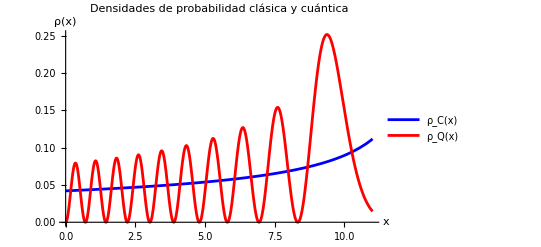

```mathematica
Plot[{rhoC[x],rhoQ[x]},{x,0,epsilonList[[9]]},PlotLabel->"Densidades de probabilidad clásica y cuántica",AxesLabel->{"x","ρ(x)"},PlotLegends->{"ρ_C(x)","ρ_Q(x)"},PlotStyle->{Blue,Red}, PlotRange->Full]
```